```mathematica
TMAT = {{Tm0m0, Tm0m1},{Tm1m0, Tm1m1}};
psi={ψ0,ψ1};
rho=Exp[-psi]/Sum[Exp[-psi[[i]]],{i,1,2}]
```

{ⅇ^-ψ0/(ⅇ^-ψ0+ⅇ^-ψ1),ⅇ^-ψ1/(ⅇ^-ψ0+ⅇ^-ψ1)}

```mathematica
TMAT//MatrixForm
```

(Tm0m0 | Tm0m1
Tm1m0 | Tm1m1)

```mathematica
vec=TMAT.rho
```

{(ⅇ^-ψ0 Tm0m0)/(ⅇ^-ψ0+ⅇ^-ψ1)+(ⅇ^-ψ1 Tm0m1)/(ⅇ^-ψ0+ⅇ^-ψ1),(ⅇ^-ψ0 Tm1m0)/(ⅇ^-ψ0+ⅇ^-ψ1)+(ⅇ^-ψ1 Tm1m1)/(ⅇ^-ψ0+ⅇ^-ψ1)}

```mathematica
nLL=-Log[Sum[vec[[i]],{i,1,2}]]
```

-Log[(ⅇ^-ψ0 Tm0m0)/(ⅇ^-ψ0+ⅇ^-ψ1)+(ⅇ^-ψ1 Tm0m1)/(ⅇ^-ψ0+ⅇ^-ψ1)+(ⅇ^-ψ0 Tm1m0)/(ⅇ^-ψ0+ⅇ^-ψ1)+(ⅇ^-ψ1 Tm1m1)/(ⅇ^-ψ0+ⅇ^-ψ1)]

```mathematica
g1=D[nLL,ψ0]//FullSimplify
```

(ⅇ^(ψ0+ψ1) (Tm0m0-Tm0m1+Tm1m0-Tm1m1))/((ⅇ^ψ0+ⅇ^ψ1) (ⅇ^ψ1 (Tm0m0+Tm1m0)+ⅇ^ψ0 (Tm0m1+Tm1m1)))

```mathematica
g2=D[nLL,ψ1]//FullSimplify
```

(ⅇ^(ψ0+ψ1) (-Tm0m0+Tm0m1-Tm1m0+Tm1m1))/((ⅇ^ψ0+ⅇ^ψ1) (ⅇ^ψ1 (Tm0m0+Tm1m0)+ⅇ^ψ0 (Tm0m1+Tm1m1)))

```mathematica
(g1-(-g2))//FullSimplify
```

0

```mathematica
subA0={Tm0m0->0.8,Tm1m0->0.05,Tm0m1->0.1,Tm1m1->0.2}
subA1={Tm0m0->0.1,Tm1m0->0.05,Tm0m1->0.1,Tm1m1->0.6}
```

{Tm0m0→0.8,Tm1m0→0.05,Tm0m1→0.1,Tm1m1→0.2}

{Tm0m0→0.1,Tm1m0→0.05,Tm0m1→0.1,Tm1m1→0.6}

```mathematica
val = 0.79;
rhoTrue={val, 1-val}
```

{0.79,0.21}

```mathematica
probA0gM0=(Tm0m0 +Tm1m0)/.subA0
probA0gM1=(Tm0m1 +Tm1m1)/.subA0
probA1gM0=(Tm0m0 +Tm1m0)/.subA1
probA1gM1=(Tm0m1 +Tm1m1)/.subA1
```

0.85

0.3

0.15

0.7

```mathematica
probA0=probA0gM0 rhoTrue[[1]]+probA0gM1 rhoTrue[[2]]
```

0.7345

```mathematica
probA1=probA1gM0 rhoTrue[[1]]+probA1gM1 rhoTrue[[2]]
```

0.2655

```mathematica
rho/.Minimize[{probA1(nLL/.subA1)+probA0(nLL/.subA0)},{ψ0, ψ1}][[2]]
```

{1.,2.05412×10^-33}

```mathematica
rho/.Minimize[probA1(nLL/.subA1)+probA0(nLL/.subA0)+0.001Sqrt[ψ0^2+ψ1^2],{ψ0, ψ1}][[2]]
```

{0.787268,0.212732}

```mathematica
sol=Minimize[{probA1(nLL/.subA1)+probA0(nLL/.subA0),ψ0^2<10, ψ1^2<10},{ψ0, ψ1}]
```

{0.578731,{ψ0→-1.39852,ψ1→-0.0735935}}

```mathematica
rho/.sol[[2]]
```

{0.79,0.21}

```mathematica
subA0par={Tm0m0->Tm0m0A0,Tm1m0->Tm1m0A0,Tm0m1->Tm0m1A0,Tm1m1->Tm1m1A0};
subA1par={Tm0m0->Tm0m0A1,Tm1m0->Tm1m0A1,Tm0m1->Tm0m1A1,Tm1m1->Tm1m1A1};
```

```mathematica
nLLTOT=(pA1 nLL/.subA1par)+(pA0 nLL/.subA0par);
g0=D[nLLTOT,ψ0]//FullSimplify
g1=D[nLLTOT,ψ1]//FullSimplify
```

ⅇ^ψ0 ((pA0+pA1)/(ⅇ^ψ0+ⅇ^ψ1)-(pA0 (Tm0m1A0+Tm1m1A0))/(ⅇ^ψ1 (Tm0m0A0+Tm1m0A0)+ⅇ^ψ0 (Tm0m1A0+Tm1m1A0))-(pA1 (Tm0m1A1+Tm1m1A1))/(ⅇ^ψ1 (Tm0m0A1+Tm1m0A1)+ⅇ^ψ0 (Tm0m1A1+Tm1m1A1)))

ⅇ^ψ0 (-(pA0+pA1)/(ⅇ^ψ0+ⅇ^ψ1)+(pA0 (Tm0m1A0+Tm1m1A0))/(ⅇ^ψ1 (Tm0m0A0+Tm1m0A0)+ⅇ^ψ0 (Tm0m1A0+Tm1m1A0))+(pA1 (Tm0m1A1+Tm1m1A1))/(ⅇ^ψ1 (Tm0m0A1+Tm1m0A1)+ⅇ^ψ0 (Tm0m1A1+Tm1m1A1)))

```mathematica
Solve[{g0==0,g1==0},{ψ0,ψ1}]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{ψ1→-ⅈ π+ψ0-Log[-pA0 (Tm0m0A1+Tm1m0A1) (Tm0m0A0-Tm0m1A0+Tm1m0A0-Tm1m1A0)-pA1 (Tm0m0A0+Tm1m0A0) (Tm0m0A1-Tm0m1A1+Tm1m0A1-Tm1m1A1)]+Log[-pA1 (Tm0m1A0+Tm1m1A0) (Tm0m0A1-Tm0m1A1+Tm1m0A1-Tm1m1A1)-pA0 (Tm0m0A0-Tm0m1A0+Tm1m0A0-Tm1m1A0) (Tm0m1A1+Tm1m1A1)]}}

```mathematica
Minimize[nLLTOT,{ψ0,ψ1}]
```

Minimize[-pA0 Log[(ⅇ^-ψ0 Tm0m0A0)/(ⅇ^-ψ0+ⅇ^-ψ1)+(ⅇ^-ψ1 Tm0m1A0)/(ⅇ^-ψ0+ⅇ^-ψ1)+(ⅇ^-ψ0 Tm1m0A0)/(ⅇ^-ψ0+ⅇ^-ψ1)+(ⅇ^-ψ1 Tm1m1A0)/(ⅇ^-ψ0+ⅇ^-ψ1)]-pA1 Log[(ⅇ^-ψ0 Tm0m0A1)/(ⅇ^-ψ0+ⅇ^-ψ1)+(ⅇ^-ψ1 Tm0m1A1)/(ⅇ^-ψ0+ⅇ^-ψ1)+(ⅇ^-ψ0 Tm1m0A1)/(ⅇ^-ψ0+ⅇ^-ψ1)+(ⅇ^-ψ1 Tm1m1A1)/(ⅇ^-ψ0+ⅇ^-ψ1)],{ψ0,ψ1}]

```mathematica
subA0parINV={Tm0m0A0->Tm0m0,Tm1m0A0->Tm1m0,Tm0m1A0->Tm0m1,Tm1m1A0->Tm1m1}/.subA0
subA1parINV={Tm0m0A1->Tm0m0,Tm1m0A1->Tm1m0,Tm0m1A1->Tm0m1,Tm1m1A1->Tm1m1}/.subA1
```

{Tm0m0A0→0.8,Tm1m0A0→0.05,Tm0m1A0→0.1,Tm1m1A0→0.2}

{Tm0m0A1→0.1,Tm1m0A1→0.05,Tm0m1A1→0.1,Tm1m1A1→0.6}

```mathematica
psi0Test=1
psi1Test=Log[-(ⅇ (pA1 (Tm0m1A0+Tm1m1A0) (Tm0m0A1-Tm0m1A1+Tm1m0A1-Tm1m1A1)+pA0 (Tm0m0A0-Tm0m1A0+Tm1m0A0-Tm1m1A0) (Tm0m1A1+Tm1m1A1)))/(pA0 (Tm0m0A1+Tm1m0A1) (Tm0m0A0-Tm0m1A0+Tm1m0A0-Tm1m1A0)+pA1 (Tm0m0A0+Tm1m0A0) (Tm0m0A1-Tm0m1A1+Tm1m0A1-Tm1m1A1))]/.ψ0->psi0Test/.subA0parINV/.subA1parINV/.pA0->probA0/.pA1->probA1
```

1

2.32493

```mathematica
rho/.ψ0->psi0Test/.ψ1->psi1Test//FullSimplify
```

{0.79,0.21}

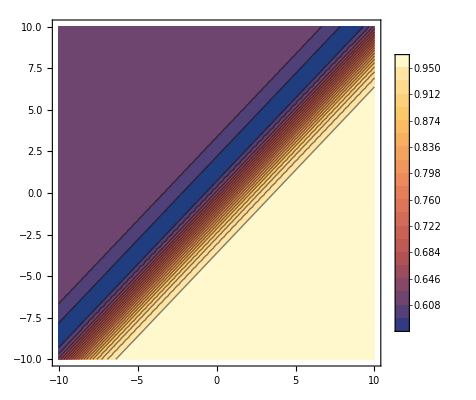

```mathematica
ContourPlot[probA1(nLL/.subA1)+probA0(nLL/.subA0),{ψ0, -10,10},{ψ1,-10,10}, PlotLegends->Automatic, Contours->20]
```

```mathematica
TMAT = {{Tm0m0, Tm0m1},{Tm1m0, Tm1m1}};
psi={1,ψ1};
rho=Exp[-psi]/Sum[Exp[-psi[[i]]],{i,1,2}]
```

{1/(ⅇ (1/ⅇ+ⅇ^-ψ1)),ⅇ^-ψ1/(1/ⅇ+ⅇ^-ψ1)}

```mathematica
TMAT//MatrixForm
```

(Tm0m0 | Tm0m1
Tm1m0 | Tm1m1)

```mathematica
vec=TMAT.rho
```

{Tm0m0/(ⅇ (1/ⅇ+ⅇ^-ψ1))+(ⅇ^-ψ1 Tm0m1)/(1/ⅇ+ⅇ^-ψ1),Tm1m0/(ⅇ (1/ⅇ+ⅇ^-ψ1))+(ⅇ^-ψ1 Tm1m1)/(1/ⅇ+ⅇ^-ψ1)}

```mathematica
nLL=-Log[Sum[vec[[i]],{i,1,2}]]
```

-Log[Tm0m0/(ⅇ (1/ⅇ+ⅇ^-ψ1))+(ⅇ^-ψ1 Tm0m1)/(1/ⅇ+ⅇ^-ψ1)+Tm1m0/(ⅇ (1/ⅇ+ⅇ^-ψ1))+(ⅇ^-ψ1 Tm1m1)/(1/ⅇ+ⅇ^-ψ1)]

```mathematica
g1=D[nLL,ψ0]//FullSimplify
```

0

```mathematica
g2=D[nLL,ψ1]//FullSimplify
```

-ⅇ/(ⅇ+ⅇ^ψ1)+(ⅇ (Tm0m1+Tm1m1))/(ⅇ^ψ1 (Tm0m0+Tm1m0)+ⅇ (Tm0m1+Tm1m1))

```mathematica
(g1-(-g2))//FullSimplify
```

-ⅇ/(ⅇ+ⅇ^ψ1)+(ⅇ (Tm0m1+Tm1m1))/(ⅇ^ψ1 (Tm0m0+Tm1m0)+ⅇ (Tm0m1+Tm1m1))

```mathematica
subA0={Tm0m0->0.8,Tm1m0->0.05,Tm0m1->0.1,Tm1m1->0.2}
subA1={Tm0m0->0.1,Tm1m0->0.05,Tm0m1->0.1,Tm1m1->0.6}
```

{Tm0m0→0.8,Tm1m0→0.05,Tm0m1→0.1,Tm1m1→0.2}

{Tm0m0→0.1,Tm1m0→0.05,Tm0m1→0.1,Tm1m1→0.6}

```mathematica
val = 0.79;
rhoTrue={val, 1-val}
```

{0.79,0.21}

```mathematica
probA0gM0=(Tm0m0 +Tm1m0)/.subA0
probA0gM1=(Tm0m1 +Tm1m1)/.subA0
probA1gM0=(Tm0m0 +Tm1m0)/.subA1
probA1gM1=(Tm0m1 +Tm1m1)/.subA1
```

0.85

0.3

0.15

0.7

```mathematica
probA0=probA0gM0 rhoTrue[[1]]+probA0gM1 rhoTrue[[2]]
```

0.7345

```mathematica
probA1=probA1gM0 rhoTrue[[1]]+probA1gM1 rhoTrue[[2]]
```

0.2655

```mathematica
rho/.Minimize[{probA1(nLL/.subA1)+probA0(nLL/.subA0)},{ψ1}][[2]]
```

{0.79,0.21}

```mathematica
rho/.Minimize[probA1(nLL/.subA1)+probA0(nLL/.subA0)+0.001Sqrt[ψ0^2+ψ1^2],{ψ0, ψ1}][[2]]
```

{0.787268,0.212732}

```mathematica
sol=Minimize[{probA1(nLL/.subA1)+probA0(nLL/.subA0),ψ0^2<10, ψ1^2<10},{ψ0, ψ1}]
```

{0.578731,{ψ0→-1.39852,ψ1→-0.0735935}}

```mathematica
rho/.sol[[2]]
```

{0.79,0.21}

```mathematica
TMAT/.subA0//MatrixForm
```

(0.9 | 0.
0. | 0.2)

```mathematica
(TMAT/.subA1).{0.1,0.8}
```

{0.81,0.18}

```mathematica
(TMAT/.subA2).{0.1,0.8}
```

{0.27,0.72}

```mathematica
TMAT/.subA2//MatrixForm
```

(0.3 | 0.3
0.8 | 0.8)

```mathematica
Sum[vec[[i]],{i,1,2}]/.subA1
```

(1.1 ⅇ^-ψ1)/(ⅇ^-ψ1+ⅇ^-ψ2)+(1.1 ⅇ^-ψ2)/(ⅇ^-ψ1+ⅇ^-ψ2)

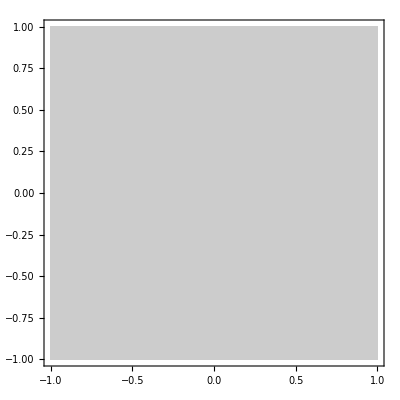

-Graphics-

```mathematica
ContourPlot[nLL/.subA1,{ψ1,-1,1},{ψ2,-1,1}, PlotLegends->Automatic]
ContourPlot[nLL/.subA2,{ψ1,-1,1},{ψ2,-1,1}, PlotLegends->Automatic]
```

```mathematica
Minimize[(nLL/.subA1)+(nLL/.subA2),{ψ1, ψ2}]
```

{-0.19062,{ψ1→-0.535769,ψ2→-0.13703}}

```mathematica
rho/.{ψ1->-0.5357689240245056,ψ2->-0.13703001527149958}
```

{0.598385,0.401615}

```mathematica
Minimize[Sum[vec[[i]],{i,1,2}]/.{T11->0.9,T12->0.4,T21->0.2,T22->0.1},{ψ1, ψ2}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::munfl: Exp[-2487.63] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-918.696] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NMinimize::nnum: The function value Indeterminate is not a number at {ψ1,ψ2} = {2487.63,918.696}.

{0.5,{ψ1→68.5813,ψ2→12.123}}

```mathematica
rho/.{ψ1->68.58131422278939,ψ2->12.123007334406452}
```

{3.02321×10^-25,1.}